```mathematica
StringJoin[IntegerString[FromDigits[#,16],16,2]&/@StringSplit["74, 0, 0, 0, a1, da, f, 98, 84, 1, 33, 29, b9, cd, 61, d8, 63, 16, a7, 60, 76, 5, 13, c8, ed, d2, 1f, 69, 50, 3c, b6, 6c, 45",", "]]
```

74000000a1da0f9884013329b9cd61d86316a760760513c8edd21f69503cb66c45

```mathematica
Length[StringSplit["74, 0, 0, 0, a1, da, f, 98, 84, 1, 33, 29, b9, cd, 61, d8, 63, 16, a7, 60, 76, 5, 13, c8, ed, d2, 1f, 69, 50, 3c, b6, 6c, 45",", "]]
```

33

```mathematica
S
```

```mathematica
StringPartition["7400966969ac9246132060abdbe8e501217589da059cdaa8ff4704d76f7014b3a1",2]
```

{74,00,96,69,69,ac,92,46,13,20,60,ab,db,e8,e5,01,21,75,89,da,05,9c,da,a8,ff,47,04,d7,6f,70,14,b3,a1}

```mathematica
FromDigits["0e",16]
```

14

```mathematica
FromCharacterCode@FromDigits["74",16]
```

t

```mathematica
ToCharacterCode["00obfuscate_key"]
```

{48,48,111,98,102,117,115,99,97,116,101,95,107,101,121}

```mathematica
x[t_]:=1/4+(x[0]-1/4)*E^(-4 α t)
```

```mathematica
x'[t]
```

∂_t Hold[1/4+(x[0]-1/4) ⅇ^(-4 α t)]

```mathematica
Clear[x]
```

```mathematica
x[t+1]==α(1-4 x[t])+x[t]
```

```mathematica
Clear[x]
```

```mathematica
DSolve[{x[0]==c,x[t+1]==α(1-4 x[t])+x[t],x'[t+1]==α(1-4 x[t])},x,t]
```

DSolve::litarg: To avoid possible ambiguity, the arguments of the dependent variable in {x'[1+t]==α (1-4 x[t]),x[1+t]==α (1-4 x[t])+x[t]} should literally match the independent variables.

DSolve[{x[0]==c,x[1+t]==α (1-4 x[t])+x[t],x'[1+t]==α (1-4 x[t])},x,t]

```mathematica
Expand@NestList[Function[prev,α(1-4 prev)+prev],c,5]
```

{c,c+α-4 c α,c+2 α-8 c α-4 α^2+16 c α^2,c+3 α-12 c α-12 α^2+48 c α^2+16 α^3-64 c α^3,c+4 α-16 c α-24 α^2+96 c α^2+64 α^3-256 c α^3-64 α^4+256 c α^4,c+5 α-20 c α-40 α^2+160 c α^2+160 α^3-640 c α^3-320 α^4+1280 c α^4+256 α^5-1024 c α^5}

```mathematica
RSolveValue[{x[0]==c,x[t+1]-x[t]==α(1-4 x[t])},x[t],t]
```

1/4 (1-(1-4 α)^t+4 c (1-4 α)^t)

```mathematica
1/4+(c-1/4)*Exp[-4α t]==RSolveValue[{x[0]==c,x[t+1]-x[t]==α(1-4 x[t])},x[t],t]/.c->1/4
```

True

```mathematica
Solve[1/4+(c-1/4)*Exp[-4α t]==RSolveValue[{x[0]==c,x[t+1]-x[t]==α(1-4 x[t])},x[t],t],c]
```

{{c→1/4}}

```mathematica
FullSimplify[1/4+(c-1/4)*Exp[-4α t]==RSolveValue[{x[0]==c,x[t+1]-x[t]==α(1-4 x[t])},x[t],t]]
```

(-1+4 c) ⅇ^(-t α) (-1+ⅇ^(4 t α) (1-4 α)^t)==0

```mathematica
D[x[t+1]]
```

x[1+t]

```mathematica
1/4 (1-(1-4 α)^t+4 c (1-4 α)^t)/.c->5
```

1/4 (1+19 (1-4 α)^t)

```mathematica
867.72/60
```

14.462

```mathematica
processStr[str_]:={FromUnixTime[#[[1]]],#[[2]],#[[3]]}&/@Map[ToExpression,StringSplit[StringCases[str,Shortest["("~~c__~~")"]:>c],", "],{2}]
```

```mathematica
str1=;
```

```mathematica
ts=processStr[str1];
```

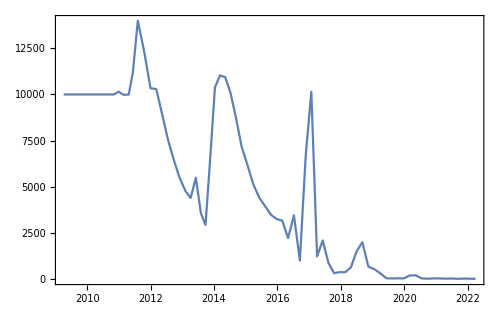

```mathematica
DateListPlot[ts[[All,{1,3}]]]
```

```mathematica
str2=;
```

```mathematica
ts2=processStr[str2];
```

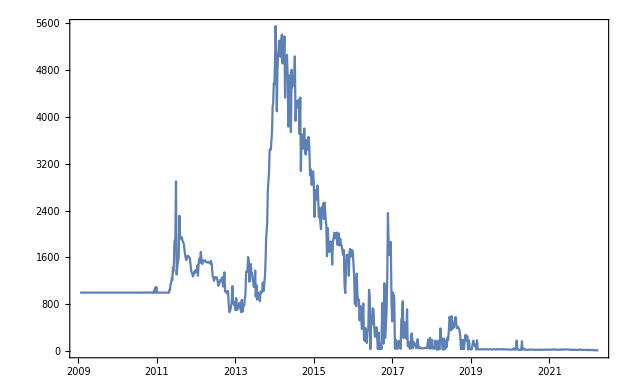

```mathematica
DateListPlot[ts2[[All,{1,3}]]]
```

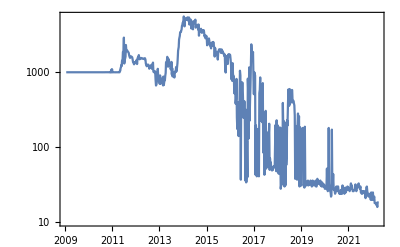

```mathematica
DateListLogPlot[ts2[[All,{1,3}]]]
```

```mathematica
((((m*2)+10)/2)-m)//FullSimplify
```

5

```mathematica
FullSimplify[(((y+3)+If[g,4,5])-y)*2-If[g,5,7]]
```

9

```mathematica
str3=;
```

```mathematica
ts3=processStr[str3];
```

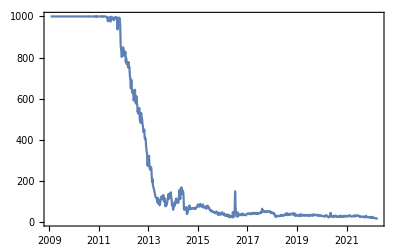

```mathematica
DateListPlot[ts3[[All,{1,3}]]]
```

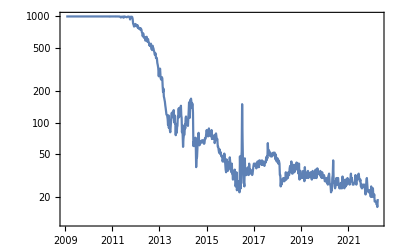

```mathematica
DateListLogPlot[ts3[[All,{1,3}]]]
```

```mathematica
str4=;
```

```mathematica
ts4=processStr[str4];
```

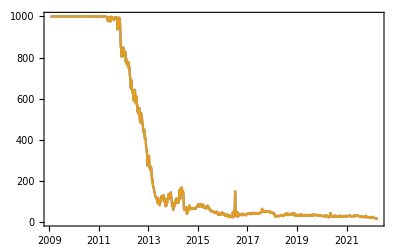

```mathematica
DateListPlot[{ts3[[All,{1,3}]],ts4[[All,{1,3}]]}]
```

```mathematica
str5=;
```

```mathematica
ts5=processStr[str5];
```

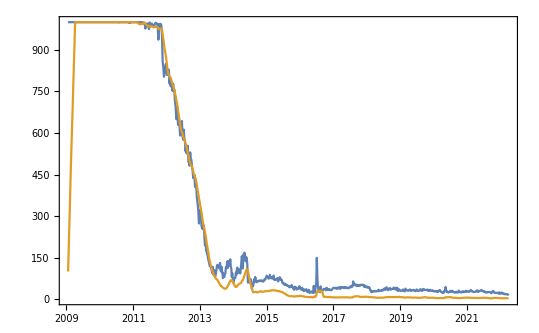

```mathematica
DateListPlot[{ts3[[All,{1,3}]],TimeSeries[ts5[[All,{1,3}]]]/10}]
```

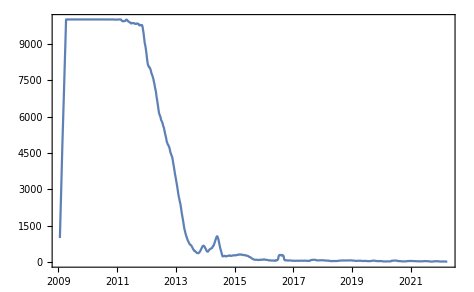

```mathematica
DateListPlot[ts5[[All,{1,3}]]]
```

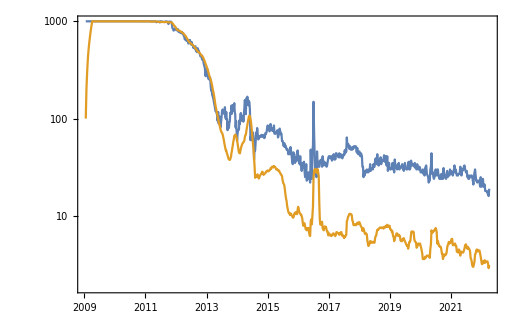

```mathematica
DateListLogPlot[{ts3[[All,{1,3}]],TimeSeries[ts5[[All,{1,3}]]]/10}]
```

```mathematica
str6=;
```

```mathematica
ts6=processStr[str6];
```

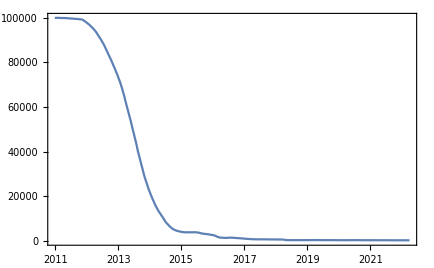

```mathematica
DateListPlot[ts6[[All,{1,3}]]]
```

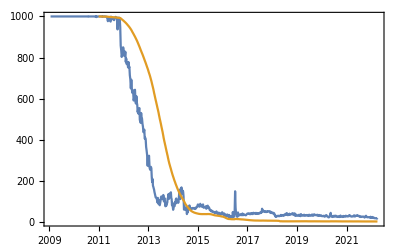

```mathematica
DateListPlot[{ts3[[All,{1,3}]],TimeSeries[ts6[[All,{1,3}]]]/100}]
```

```mathematica
resultDirectory="~/git/bitcoin-rs-experiments/results/";
```

```mathematica
transactionSizeDistribution=UnitConvert[WeightedData@@MapAt[Quantity[#,"Satoshis"]&,Transpose@Import[FileNameJoin[{resultDirectory,"transaction_size_distribution.json"}]],1],"Bitcoins"]
```

WeightedData[…]

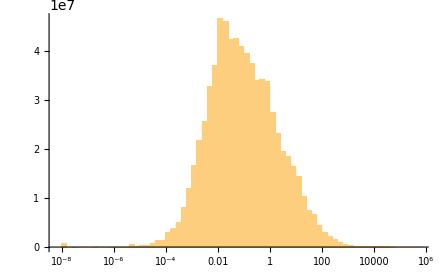

```mathematica
Histogram[transactionSizeDistribution,{"Log",75}]
```

```mathematica
transactionSizeDistributionUsd=WeightedData@@MapAt[Quantity[#,"USDollars"]&,Transpose@Import[FileNameJoin[{resultDirectory,"transaction_size_distribution_usd.json"}]],1]
```

WeightedData[…]

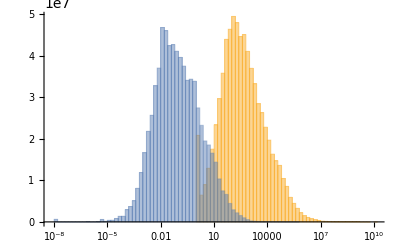

```mathematica
Histogram[{QuantityMagnitude[transactionSizeDistributionUsd],QuantityMagnitude[transactionSizeDistribution]},{"Log",75}]
```

```mathematica
FindDistribution[QuantityMagnitude[transactionSizeDistributionUsd,"USDollars"]]
```

FindDistribution::wrgfmt: Argument WeightedData[Automatic,{{1.03039×10^6,501187.,43.0527,1013.91,14655.5,414000.,3.81066,972.747,8.59014,5.50808,«9251»},{8996,15596,210672,233264,90033,18196,49251,223030,87484,67495,«9251»}}] at position 1 does not have the right format. Data should be a numerical array of depth less than 2.

FindDistribution[WeightedData[…]]

```mathematica
transactionVolume=TimeSeries[{FromUnixTime[#1],Quantity[#2,"Satoshis"]}&@@@Import[FileNameJoin[{resultDirectory,"transaction_volume_time_series.json"}]]];
```

```mathematica
DateListPlot[MovingMap[Total,transactionVolume,"Month"],PlotRange->All]
```

-Graphics-

```mathematica
transactionVolumeUsd=QuantityMagnitude[transactionVolume,"Satoshis"]*CurrencyConvert[Quantity[1,"Satoshis"],"USDollars",All]
```

TimeSeries[…]

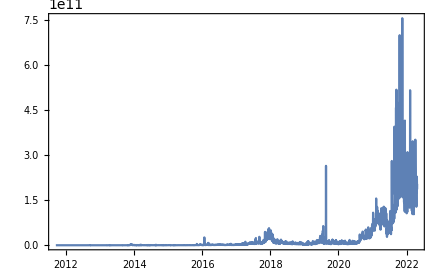

```mathematica
DateListPlot[transactionVolumeUsd,PlotRange->All]
```

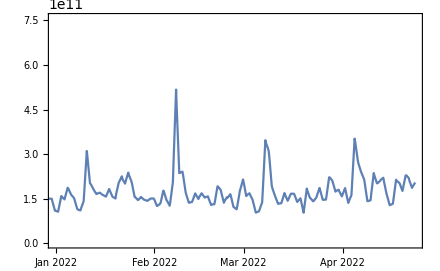

```mathematica
DateListPlot[transactionVolumeUsd,PlotRange->{{DateObject[{2022,1,1}],All},All}]
```

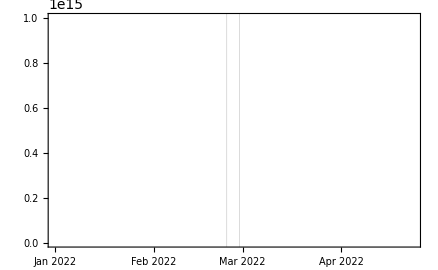

```mathematica
DateListPlot[transactionVolume,PlotRange->{{DateObject[{2022,1,1}],All},{0,1.5*10^15}},GridLines->{{{2022,2,24},{2022,2,28}},None}]
```

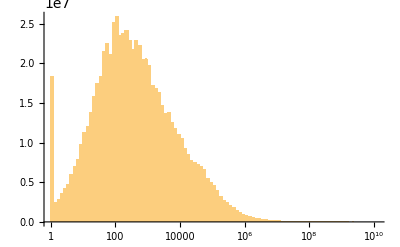

```mathematica
Histogram[transactionSizeDistributionUsd,{"Log",75},PlotRange->All,GridLines->{{1000000},None}]
```

```mathematica
largeTransactionCount=TimeSeries[{FromUnixTime[#1],#2}&@@@Import[FileNameJoin[{resultDirectory,"large_transaction_count_time_series_1000000.json"}]]];
```

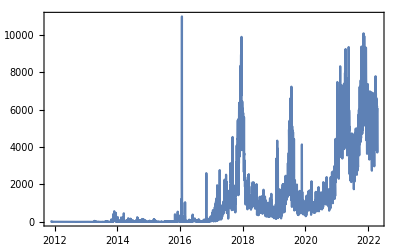

```mathematica
DateListPlot[largeTransactionCount,PlotRange->All]
```

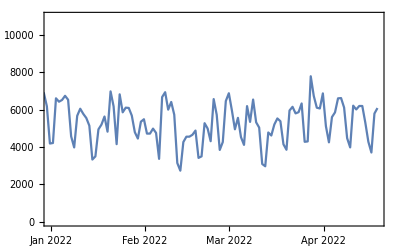

```mathematica
DateListPlot[largeTransactionCount,PlotRange->{{{2022,1,1},All},All}]
```

```mathematica
Histogram[transactionSizeDistributionUsd,{"Log",75},PlotRange->All,GridLines->{{100000},None}]
```

-Graphics-

```mathematica
largeTransactionCount2=TimeSeries[{FromUnixTime[#1],#2}&@@@Import[FileNameJoin[{resultDirectory,"large_transaction_count_time_series_100000.json"}]]];
```

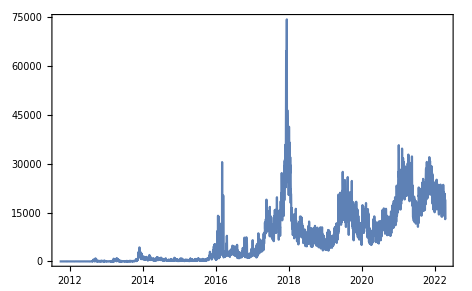

```mathematica
DateListPlot[largeTransactionCount2,PlotRange->All]
```

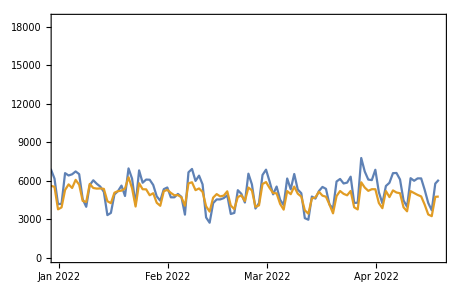

```mathematica
DateListPlot[{largeTransactionCount,largeTransactionCount2/4},PlotRange->{{{2022,1,1},All},All}]
```

## Exchange rates table

```mathematica
ts=TimeSeriesResample[CurrencyConvert[Quantity[1,"Satoshis"],"USDollars",All],"Day"];
```

```mathematica
CopyToClipboard@StringRiffle[MapThread[StringTemplate["exchange_rates.insert(chrono::Date::<Utc>::from_utc(chrono::NaiveDate::from_ymd(``,``,``), Utc), ``);"],{DateValue[ts["Dates"],"Year"],DateValue[ts["Dates"],"Month"],DateValue[ts["Dates"],"Day"],QuantityMagnitude[ts["Values"],"USDollars"]}],"\n"]
```